# 医学生物学分野における高被引用論文の長期変化

## 要旨

本研究では医学生物学分野における引用関係と主要テーマの長期変化を、年代ごとの高被引用論文に着目することによって明らかにする。年代ごとのデータを累積的に構成することにより引用関係の変化と長期的トレンドを追跡する。

## 背景

長期にわたる大規模な引用関係の分析は、主に雑誌間の関係に注目されることが多かった。比較的大規模な研究としては、Leydesdorff[1,2,3,4]が雑誌間の関係マップを構築・調査した。天野ら[5,6]は医学生物学雑誌の大規模クラスタリングを行い、分野間の引用関係を明らかにしている。近年ではLiら[7]が長期にわたる引用の特徴を、2300万論文をグループ化して調査した。しかしながら長期にわたる論文の引用関係と研究のトレンドに着目した研究は稀である。そこで本研究ではPubMedのデータを利用し医学生物学分野の高被引用論文に注目し、引用関係の年代ごとの変化を調査した。

高被引用論文は研究のトレンドをよく反映するものと考えられ、またPubMedには各論文に統制語が付与されているため、高被引用論文に付与される統制語を計量的に分析することにより、トレンド変化の特徴を見出せると期待される。

## 目的

本研究ではとくに長期的なトレンドに注目する。この目的のために一部の分析では累積的なデータを利用した。これにより一過的なトレンドは現れにくくなると期待される。1940年代から近年にかけての医学生物学分野における主要論文とこれらの引用関係・主要雑誌・主要テーマの推移を、巨大なレファレンスネットワークを年代ごとに構成・分析することによって明らかにする。主要論文とは累積年代ごとの上位1%の被引用数を持つ論文集合であり、主要雑誌とは当該論文を出版した雑誌であり、主要テーマとは当該論文に付与されたMeSHおよびその論文を引用する論文に付与されたMeSHに対応する分野である。トレンドの長期的な流れを汲むことを主眼とし、レファレンスネットワークは累積的に構成する。

## 方法

### 1. データ

PubMed[8]のFTP版データ2023ベースラインを利用した。

### 2. 年代の構成

FTP版 PubMed 2023ベースラインに収録されている出版年が1946-2020の論文を対象とした。オーバーラップなしの5年ごとの区切りとし、15世代のレファレンスネットワークを構成した。対象となる被引用論文はベースラインに収録される最初の出版年（1781）から当該年代までのすべてのタイプの記事となる。

### 3. 主要論文・主要雑誌・主要テーマ

ここで本研究におけるトレンドを定義する。まずトレンドとは主要論文、主要雑誌、主要テーマである。次に三者を定義する。主要論文とは、各年代において、被引用数における上位の論文であり、被引用数全体の1%を構成する被引用数上位の論文集合とする。被引用数1%に対する厳密な抽出は困難であるため、被引用数の多い順に論文の被引用数を累積し、全引用数の1%に最も近い順位を持つ論文までを対象とした。主要雑誌とは主要論文を出版した雑誌とする。主要テーマとは主要論文に付与されるNeSHおよび主要論文を引用する論文に付与されるNeSHの集合とする。

年代とは上記の通り論文の出版年代であり、このデータを累積的に用いた場合は累積年代と称する。図表においては最終年を表記するか期間を明記する。

以上の定義を表1にまとめる。

表1

本研究での用語定義

主要論文 | 被引用数全体の1%を構成する被引用数上位論文（集合）。
主要雑誌 | 主要論文を出版した雑誌。
主要テーマ | 主要論文に付与されるMeSHおよびその論文を引用する論文に付与されるMeSH。
年代 | 1946 - 2020の期間に対して5年ごとに区切るもの。データを累積的に扱う場合は「累積年代」と表記する。

#### 3.1 主要テーマの計数

前述の通り主要テーマには引用される論文のテーマおよび引用する論文のテーマが定義される。これらの単独の計数についてはそれぞれ主要論文に付与されるMeSHディスクリプター、要論文を引用する論文に付与されるMeSHディスクリプターを用いる。一方、テーマ間の引用関係の計数は以下のように行う。一対の論文の引用関係をディスクリプター集合間の引用関係ととらえ、これを被引用側・引用側における完全2部グラフの関係とみなす。

## 結果

### 1. PubMed annual baseline

本研究で用いた2023年のFTP版PubMed annual baselineの概要を表2に示す。わずかに2024年の論文も含まれている。

図1に出版年ごとの論文収録数を示す。1945年から明確な増加が見られる。

表 2

PubMed annual baselineのレコード数

Article count | ISSN count | First publish year | Last publish year
36,555,430 | 36,943 | 1781 | 2024

図1に出版年ごとの論文収録数を示す。1945年から明確な増加が見られる。

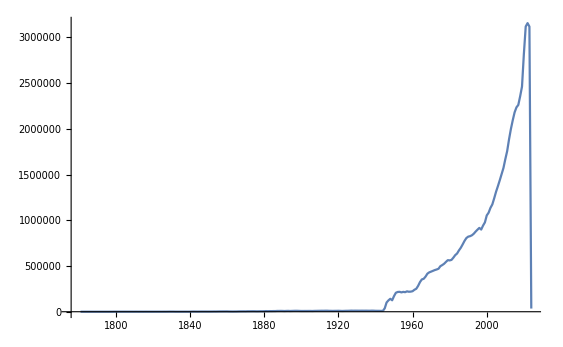

図1

PubMed annual baselineの登録論文数の推移

### 2. 年代ごとの論文数

図2に年代ごとの論文数、うち参照を持つ論文数、参照数（述べ）、被引用論文数（ユニーク）、登録雑誌数を示す。登録雑誌数以外は2005から2010にかけ急激な指数関数的増加を示している。

図3に累積年代ごとの被引用数とそのランクを、Zipfの式 [c r^(-a)] に回帰させた場合の係数aの推移を示す。係数aは1946-1980の年代をピークに前半では上昇傾向、後半では下降傾向にある。いずれの値も1未満であり学術活動に一般的に見られる冪乗則における値よりも小さい。

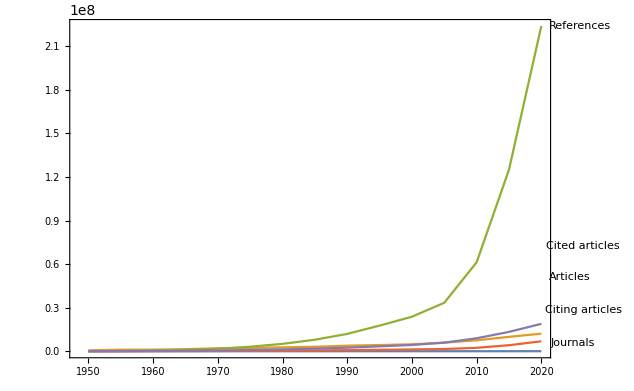

図 2

年代ごとの論文数：

年代ごとの論文数(articles)、うち参照を持つ論文数(citing articles)、参照数(references)、被引用論文数(cited articles)、および雑誌数(Journal)。

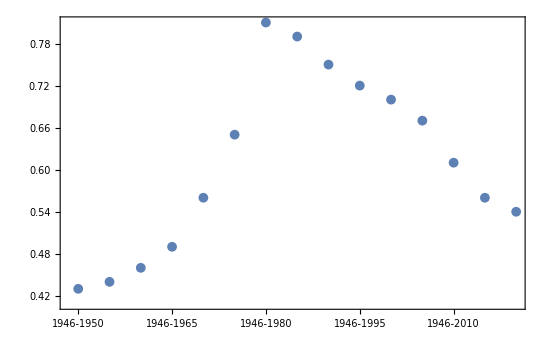

図3

累積年代ごとの被引用数におけるZipfの係数aの値

### 3. 累積年代ごとの主要論文の変化

累積年代ごとの最多被引用論文の論文タイトルとその被引用数を表3に示す。主要論文は年代が進んでも引き続き引用され続ける傾向があり、このため累積的変化では複数年代にわたり最多被引用主要論文の交代は少ない。いずれの論文のテーマもタンパク質の分析に関するものであり、後者2タイトルは出版後10年から数十年をかけてインパクトを上昇させている。

最初の年代を除く主要論文の新規出現数を表4に示す。主要論文における新規論文の出現は一定でなく増減における傾向も見られない。2006から2020の3世代では主要論文数そのものが急増しているが、これは収録論文数の急増を受けてのものであると考えられる。

表 3

累積年代ごとの最多被引用論文タイトル

Generation | Article title | Journal | Publish year | cited count
1946-1950 | Qualitative analysis of proteins: a partition chromatographic method using paper | Biochem J. | 1944 | 74
1946-1955 | Qualitative analysis of proteins: a partition chromatographic method using paper | Biochem J. | 1944 | 154
1946-1960 | Protein measurement with the Folin phenol reagent | J Biol Chem. | 1951 | 300
1946-1965 | Protein measurement with the Folin phenol reagent | J Biol Chem. | 1951 | 1190
1946-1970 | Protein measurement with the Folin phenol reagent | J Biol Chem. | 1951 | 3876
1946-1975 | Protein measurement with the Folin phenol reagent | J Biol Chem. | 1951 | 9632
1946-1980 | Protein measurement with the Folin phenol reagent | J Biol Chem. | 1951 | 17763
1946-1985 | Protein measurement with the Folin phenol reagent | J Biol Chem. | 1951 | 25451
1946-1990 | Protein measurement with the Folin phenol reagent | J Biol Chem. | 1951 | 32371
1946-1995 | Protein measurement with the Folin phenol reagent | J Biol Chem. | 1951 | 37576
1946-2000 | Protein measurement with the Folin phenol reagent | J Biol Chem. | 1951 | 40229
1946-2005 | Protein measurement with the Folin phenol reagent | J Biol Chem. | 1951 | 42101
1946-2010 | Protein measurement with the Folin phenol reagent | J Biol Chem. | 1951 | 44884
1946-2015 | Cleavage of structural proteins during the assembly of the head of bacteriophage T4 | Nature. | 1970 | 49961
1946-2020 | Cleavage of structural proteins during the assembly of the head of bacteriophage T4 | Nature. | 1970 | 54249

表4

累積年代ごとの主要論文におけるの新規主要論文出現

Generation | Newcomer | Newcomer % | Top 1% article
1946-1950 | - | - | 10
1946-1955 | 22 | 73. | 30
1946-1960 | 25 | 54. | 46
1946-1965 | 20 | 40. | 50
1946-1970 | 9 | 24. | 38
1946-1975 | 7 | 21. | 33
1946-1980 | 8 | 25. | 32
1946-1985 | 10 | 38. | 26
1946-1990 | 2 | 11. | 19
1946-1995 | 5 | 23. | 22
1946-2000 | 6 | 18. | 33
1946-2005 | 27 | 41. | 66
1946-2010 | 123 | 64. | 192
1946-2015 | 158 | 50. | 315
1946-2020 | 104 | 31. | 336

### 4. 累積年代ごとの主要雑誌の変化

累積年代ごとの主要論文を出版した雑誌のうち当該論文における最大出版数を持つものの一覧を表5に示す。主要論文を持つ雑誌は必ずしもインパクトファクターが高い雑誌ではないことがわかる。

表5

累積年代ごとの主要雑誌のうち主要論文の最大出版数を持つもの：

インパクトファクター(IF)とその発表年については当該誌の公式ホームページから求めた。

Generation | Journal title (article count) IF / IFyear | Top 1% Journal
1946-1950 | The journal of clinical investigation | (3) | 13.3 | / | 2023
Biochemical journal | (3) | 4.4 | / | 2023 | 5
1946-1955 | Biochemical journal | (13) | 4.4 | / | 2023 | 11
1946-1960 | Biochemical journal | (11) | 4.4 | / | 2023 | 19
1946-1965 | Biochemical journal | (13) | 4.4 | / | 2023 | 16
1946-1970 | Biochemical journal | (9) | 4.4 | / | 2023 | 14
1946-1975 | The Journal of biological chemistry | (7) | 4. | / | 2023 | 18
1946-1980 | The Journal of biological chemistry | (7) | 4. | / | 2023 | 20
1946-1985 | The Journal of biological chemistry | (5) | 4. | / | 2023 | 17
1946-1990 | The Journal of biological chemistry | (4) | 4. | / | 2023 | 12
1946-1995 | The Journal of biological chemistry | (4) | 4. | / | 2023 | 13
1946-2000 | Journal of Molecular Biology | (4) | 4.7 | / | -
Proceedings of the National Academy of Sciences of the United States of America | (4) | 9.4 | / | 2023 | 19
1946-2005 | Proceedings of the National Academy of Sciences of the United States of America | (8) | 9.4 | / | 2023 | 28
1946-2010 | Proceedings of the National Academy of Sciences of the United States of America | (14) | 9.4 | / | 2023
Nature | (14) | 50.5 | / | 2023 | 83
1946-2015 | Nature | (20) | 50.5 | / | 2023 | 136
1946-2020 | Bioinformatics | (17) | 4.4 | / | 2023 | 145

### 5. 累積年代ごとの主要テーマの変化

#### 5.1 主要論文のテーマの変化

累積年代ごとの主要論文に付与されたMeSHディスクリプターの種数を図4に示す。ディスクリプターが大規模であるため出現数（被引用数）上位25%のものを記載した。後半の年代では種数が減少傾向にあるが、これは新しい論文が十分に引用されないためであると考えられる。新規MeSHディスクリプターの出現の傾向は全体での傾向と一致が見られるが、出現の割合にはばらつきがあり、一定でもなく特段の傾向も見られない。

主要論文に付与されたMeSHディスクリプターの出現数に関して、年代ごとのジニ係数を図5に示す。ジニ係数には上昇傾向が見られることから特に関心が持たれるテーマに関しては年々集中する傾向がある可能性を示している。

主要論文に付与されたMeSHディスクリプターを表6に示す。ディスクリプターの出現が多いため表には出現数上位25%を占める出現数上位のディスクリプターのみ記載した。新規出現を含む上位ディスクリプター全体で見た場合、年代が累積的であるのでトレンドがやや遅れ気味に見られる。たとえば”Genetic”や”DNA”といったゲノム科学に関するタームの出現は1980年代より見られる。一方で、短期的な強い影響や他分野に属するタームの出現も見られる。例えば”COVID-19”や、”Data”や”Software”といった情報学分野のタームを含むディスクリプターである。新規出現ディスクリプターのみを見た場合はさらに近年の特徴が際立っている。たとえば”China”や”COVID-19”、”SARS-CoV-2”といったタームの出現が著しい。

表6

累積年代ごとの主要論文に付与されたMeSHディスクリプターの出現頻度上位のもの

Generation | Top 25% descriptor from Top 1% MeSH
 {Descriptor, count} | Top 25% newcomer from Top 1% MeSH
 {Descriptor, count} | Top 1% MeSH count
 Newcomer/All
1946-1950 | {} | {} | 0/0
1946-1955 | {{Humans,290},{Chromatography,111},{Chromatography, Paper,111},{Filtration,110},{Proteins,98}} | {{Humans,290},{Chromatography,111},{Chromatography, Paper,111},{Filtration,110},{Proteins,98}} | 45/45
1946-1960 | {{Humans,797},{Proteins,640},{Electrons,503},{Microscopy,503},{Microscopy, Electron,503},{Animals,464}} | {{Electrons,503},{Microscopy,503},{Microscopy, Electron,503},{Histological Techniques,235}} | 61/96
1946-1965 | {{Microscopy, Electron,1811},{Proteins,1789},{Electrons,1473},{Microscopy,1473},{Humans,1259},{Molybdenum,1190}} | {{Staining and Labeling,785},{Coloring Agents,601},{Lead,439},{Epoxy Resins,338}} | 42/117
1946-1970 | {{Microscopy, Electron,5006},{Proteins,4744},{Molybdenum,3876},{Phenols,3876},{Plant Extracts,3876}} | {{Research,468},{Leukocytes,311},{Cell Culture Techniques,302},{Tissue Culture Techniques,302},{Cell Membrane,248},{Colon,248},{Desmosomes,248}} | 33/122
1946-1975 | {{Proteins,11363},{Molybdenum,9632},{Phenols,9632},{Plant Extracts,9632}} | {{Acrylates,725},{Chemical Phenomena,725},{Chemistry,725},{Detergents,725}} | 21/125
1946-1980 | {{Proteins,21821},{Molybdenum,17763},{Phenols,17763},{Plant Extracts,17763}} | {{Genes,2995},{Autoradiography,2972},{Carbon Isotopes,2326},{Coliphages,2326}} | 44/137
1946-1985 | {{Proteins,33413},{Molybdenum,25451},{Phenols,25451},{Plant Extracts,25451},{Tungsten Compounds,25451},{Methods,13070}} | {{DNA Restriction Enzymes,6706},{DNA-Directed DNA Polymerase,4887},{Isotope Labeling,4887},{DNA Polymerase I,3741},{DNA, Viral,3741}} | 55/143
1946-1990 | {{Proteins,42099},{Molybdenum,32371},{Phenols,32371},{Plant Extracts,32371},{Tungsten Compounds,32371},{Base Sequence,28312},{Coliphages,26512}} | {{Methionine,2840},{Pancreas,2840}} | 9/108
1946-1995 | {{Proteins,53210},{Base Sequence,50402},{Coliphages,49230},{Animals,42884},{Phenols,41491},{Methods,39095},{Autoradiography,37642},{Molybdenum,37576}} | {{Conjugation, Genetic,3927},{Genetic Vectors,3927},{Methylation,3927},{Mutation,3927},{Recombination, Genetic,3927},{Cell Line,3915}} | 30/128
1946-2000 | {{Base Sequence,66991},{Proteins,65865},{Animals,60982},{Coliphages,60475},{Methods,58438},{Autoradiography,48140},{Phenols,47788},{DNA Restriction Enzymes,44426},{Kinetics,42995}} | {{Amino Acid Sequence,6743},{Operon,5573},{Nucleic Acids,5171},{Temperature,4957},{Algorithms,3541},{Databases, Factual,3541},{Sensitivity and Specificity,3541},{Sequence Homology, Nucleic Acid,3541},{Amino Acids,3202},{Bacteriorhodopsins,3202},{Chymotrypsinogen,3202},{L-Lactate Dehydrogenase,3202},{Membrane Proteins,3202}} | 71/199
1946-2005 | {{Animals,90572},{Base Sequence,89147},{Proteins,86356},{Coliphages,74223},{Methods,71809},{DNA Restriction Enzymes,57555},{Autoradiography,54873},{DNA,52664},{Escherichia coli,52460},{Phenols,51389},{Kinetics,50093}} | {{Molecular Sequence Data,13379},{Sequence Alignment,9318},{Centrifugation, Density Gradient,4303},{Protein Structure, Secondary,4300},{Chromatography,4246},{Restriction Mapping,4206},{Genetic Engineering,4045},{Culture Techniques,3896},{Phenotype,3802},{Viscosity,3713},{Chemistry, Physical,3596},{Peroxidases,3586},{Aminoquinolines,2902},{Benzofurans,2902},{Calcium,2902},{Erythrocyte Membrane,2902},{Flow Cytometry,2902}} | 126/325
1946-2010 | {{Humans,158560},{Animals,155701},{Proteins,133209},{Base Sequence,123202},{Coliphages,85105},{Methods,83913},{Software,79485},{Escherichia coli,77175},{Genes,75323},{DNA,74117},{DNA Restriction Enzymes,69150},{Kinetics,60426},{Amino Acid Sequence,59928},{Autoradiography,59757},{Phenols,55516},{Algorithms,53606}} | {{Female,24979},{Sequence Analysis, DNA,20733},{Adult,19465},{Middle Aged,17273},{Internet,16645},{Crystallography, X-Ray,14683},{Evolution, Molecular,14640},{Aged,14540},{User-Computer Interface,12740},{Reproducibility of Results,11991},{Genome, Human,11188},{Magnetic Resonance Spectroscopy,10362},{Polymerase Chain Reaction,9706},{Neoplasms,9515},{Adolescent,9460},{United States,8930},{Computer Simulation,8862},{Risk Factors,8269},{Statistics as Topic,8210},{Depression,7557},{Likelihood Functions,7073},{Protein Conformation,6953},{Reverse Transcriptase Polymerase Chain Reaction,6532},{DNA Primers,6330},{Diagnosis, Differential,6237},{Gene Duplication,6186},{Data Interpretation, Statistical,6058},{Insulin,5980},{Bipolar Disorder,5963},{Proteome,5961},{Cell Membrane,5867},{Psychiatric Status Rating Scales,5847},{CpG Islands,5769},{Human Genome Project,5755}} | 550/875
1946-2015 | {{Humans,528325},{Animals,303404},{Software,232535},{Proteins,190391},{Algorithms,184962},{Female,166214},{Base Sequence,150466},{Male,145741},{Adult,127585},{Amino Acid Sequence,118275},{Molecular Sequence Data,115319},{Time Factors,112204},{Sequence Alignment,111794},{Middle Aged,104416},{Methods,96927},{DNA,93555},{Genes,91851},{Aged,86412},{Coliphages,86236},{Sequence Analysis, DNA,77119}} | {{Software Design,16245},{Sequence Analysis, RNA,15708},{Meta-Analysis as Topic,14949},{Fibroblasts,14388},{Registries,13736},{Magnetic Resonance Imaging,13212},{DNA-Binding Proteins,13109},{Research Design,12463},{Stem Cells,12199},{Image Processing, Computer-Assisted,11710},{Octamer Transcription Factor-3,10931},{Pluripotent Stem Cells,10931},{SOXB1 Transcription Factors,10931},{Lung Neoplasms,10693},{Models, Neurological,10452},{Young Adult,10448},{3' Untranslated Regions,10263},{Neurons,10023},{Regression Analysis,9972},{Amino Acid Substitution,9896},{Mesoderm,9884},{Chronic Disease,9438},{Cell Division,9283},{Teratoma,8969},{Embryo, Mammalian,8333},{Kruppel-Like Factor 4,8333},{Kruppel-Like Transcription Factors,8333},{Chemotherapy, Adjuvant,8159},{Data Mining,7987},{Mice, SCID,7618},{Randomized Controlled Trials as Topic,7501},{Internationality,7492},{Disease Progression,7344},{Computer Systems,7307},{DNA, Neoplasm,7299},{Reference Values,7199},{Nanog Homeobox Protein,7193},{Double-Blind Method,7165},{Calibration,7104}} | 468/1243
1946-2020 | {{Humans,1150488},{Software,599982},{Algorithms,487149},{Animals,442215},{Female,407929},{Male,365150},{Adult,290280},{Proteins,251658},{Middle Aged,249798},{Sequence Alignment,249667},{Neoplasms,228769},{Aged,222241},{Computational Biology,214560},{Base Sequence,204067},{Time Factors,197567}} | {{China,37829},{Coronavirus Infections,31960},{COVID-19,31960},{Pneumonia, Viral,31960},{Liver Neoplasms,20869},{Evidence-Based Practice,20007},{Periodicals as Topic,20007},{Publication Bias,20007},{Review Literature as Topic,20007},{Betacoronavirus,19663},{SARS-CoV-2,19663},{Mortality,18408},{Fever,17823},{Stomach Neoplasms,17015},{Radiography, Thoracic,16754},{Datasets as Topic,15864}} | 217/1178

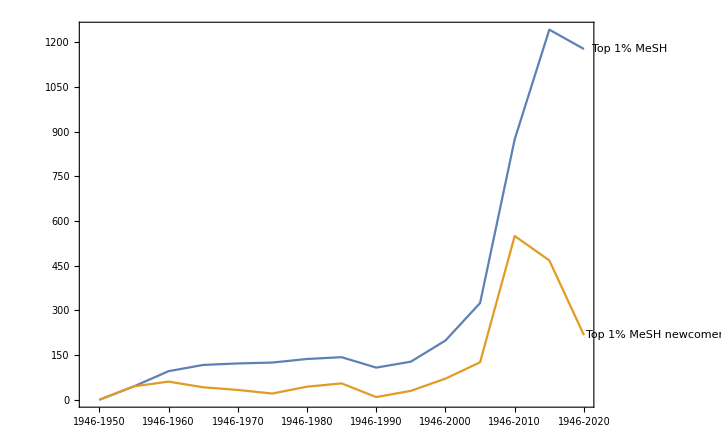

図4

累積年代ごとの主要論文に付与されたMeSHディスクリプターの種数

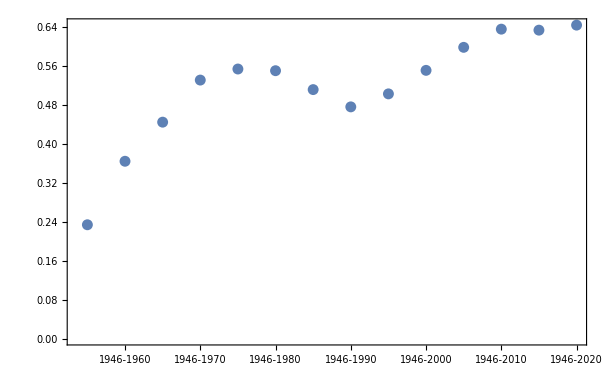

図5

累積年代ごとの主要論文に付与されたMeSHディスクリプターの出現数に関するジニ係数

#### 5.2 主要論文を引用する論文のテーマの変化

主要論文を引用する論文に付与されたMeSHディスクリプターの種数を図6に示す。引用される論文ではないので引用までの期間にかかる影響を受けず調査期間を通して一定の上昇傾向にある。新規出現するディスクリプターはほぼ毎年同じ数が見られる。

主要論文を引用する論文に付与されたMeSHディスクリプターの出現数に関して、年代ごとのジニ係数を図7に示す。ジニ係数には主要論文のそれと同じ上昇傾向が見られる。

主要論文を引用する論文に付与されたMeSHディスクリプターを表7に示す。ディスクリプターが大規模であるため出現数（引用数）上位25%のものを記載した。ディスクリプターの種数としては主要論文のものと比べ相当多く（主要論文のものの数倍）、高被引用となるテーマは他のざまざまなテーマから引用されるであろうという直観と一致する。表6と表7より出現数上位となるディスクリプターを比較すると、表7がより分野の広さを反映している傾向は見られるものの、かなり一般的な”Humans”や”Animals”といったディスクリプターが多見される特徴は同様である。新規出現するディスクリプターの割合は表7の方がかなり少ない。

表7

Generation | Top 25% descriptor from Top 1% MeSH
 {Descriptor, count} | Top 25% newcomer from Top 1% MeSH
 {Descriptor, count} | Top 1% MeSH count
 Newcomer/All
1946-1950 | {{Humans,112},{Bacteria,34},{Animals,32},{Escherichia coli,25},{Kidney,21},{Mutation,15},{Blood,14},{Bacteriophages,13},{Male,13}} | {{Humans,112},{Bacteria,34},{Animals,32},{Escherichia coli,25},{Kidney,21},{Mutation,15},{Blood,14},{Bacteriophages,13},{Male,13}} | 434/434
1946-1955 | {{Humans,612},{Animals,282},{Amino Acids,139},{Proteins,89},{Liver,83},{Bacteria,81},{Electrophoresis,79},{Chromatography,78},{Blood,71},{Oxidation-Reduction,69},{Blood Proteins,60},{Brain,60},{Rats,58},{Kidney,55},{Escherichia coli,49},{Male,47},{Muscles,44}} | {{Electrophoresis,79},{Brain,60},{Electrophoresis, Paper,41},{Carbohydrate Metabolism,39},{Polysaccharides,27},{Muscle Relaxants, Central,25},{Cerebrovascular Circulation,24},{Nucleotides,23},{Epinephrine,21},{Cardiovascular Agents,19},{Cytochromes,19},{Esterases,19},{Mitochondria,19},{Sheep,19},{Norepinephrine,18},{Sheep, Domestic,18},{Sweetening Agents,17},{Adenosine Triphosphate,16},{Immunochemistry,16},{Ions,16},{Anemia, Sickle Cell,15},{Cerebrospinal Fluid,15},{Lipid Metabolism,15},{Hexamethonium,14},{Neurons,13},{Pseudomonas,13},{Rumen,13},{Amino Acid Sequence,12},{Insecta,12},{Metabolism,12},{Acetates,11},{Bis-Trimethylammonium Compounds,11},{Cytochromes c,11},{Fructose,11},{Glutamates,11},{Hexoses,11},{Mammals,11},{Oxidative Phosphorylation,11},{Peptide Hydrolases,11},{Phosphorus Compounds,11},{Breast,10},{Cell Respiration,10},{Fermentation,10},{Glycoside Hydrolases,10},{Nerve Fibers,10}} | 1193/1596
1946-1960 | {{Humans,1499},{Animals,1282},{Microscopy, Electron,471},{Electrons,429},{Microscopy,393},{Muscles,273},{Rats,269},{Cytoplasm,262},{Proteins,257},{Amino Acids,240},{Mitochondria,210},{Liver,207},{Histological Techniques,192},{Blood Proteins,155},{Neurons,151}} | {{Endoplasmic Reticulum,121},{Cell Membrane,82},{Golgi Apparatus,74},{Epithelium,40},{Synapses,39},{Vacuoles,30},{Capillaries,28},{Epithelial Cells,28},{Microsomes,27},{Properdin,27},{Cytoskeleton,26},{Poliovirus,26},{Fluorescent Antibody Technique,25},{Complement System Proteins,24},{Nuclear Envelope,24},{Spermatids,24},{Basement Membrane,22},{HeLa Cells,18},{Immunoglobulins,17},{Organelles,17},{Stem Cells,17},{Cell Division,16},{Endothelium,16},{Aldosterone,15},{Ganglia, Spinal,15},{Histology,15},{Microscopy, Phase-Contrast,15},{Research Design,15},{Adenine,14},{Immunologic Tests,14},{Microsomes, Liver,14},{Microvilli,14},{Pinocytosis,14},{Protein Biosynthesis,14},{Spermatogenesis,14},{Cytodiagnosis,13},{Endoplasmic Reticulum, Rough,13},{Antigen-Antibody Reactions,12},{Cell Biology,12},{Epidermis,12},{Lupus Erythematosus, Systemic,12},{Mechanoreceptors,12},{Muscle Fibers, Skeletal,12},{Nissl Bodies,12},{Oocytes,12}} | 1484/3000
1946-1965 | {{Animals,3098},{Humans,2091},{Research,1618},{Microscopy, Electron,1568},{Electrons,1112},{Microscopy,1058},{Rats,954},{In Vitro Techniques,720},{Cytoplasm,666},{Proteins,648},{Liver,625},{Mitochondria,483},{Amino Acids,442},{Escherichia coli,423},{Muscles,411},{Rabbits,404},{RNA,378},{DNA,363}} | {{Carbon Isotopes,135},{RNA, Bacterial,90},{DNA, Bacterial,88},{Ultracentrifugation,86},{Toxicology,70},{Immunodiffusion,57},{Virus Cultivation,49},{Haptoglobins,45},{Drug Resistance, Microbial,44},{Glycerides,44},{RNA, Messenger,44},{Thymidine,41},{Chromatography, Gel,40},{Dactinomycin,39},{Animals, Newborn,34},{Ligases,34},{Phosphorus Isotopes,34},{Galactosidases,31},{Dietary Fats,29},{Puromycin,29},{RNA, Viral,28},{DNA, Viral,27},{Enzyme Inhibitors,27},{Chemical and Drug Induced Liver Injury,26},{Chromatography, Thin Layer,26},{Culture Techniques,26},{Glucose-6-Phosphatase,26},{Electron Transport,23},{Dialysis,22},{Genes,22},{Saccharomyces,22},{Escherichia coli K12,21},{Nucleotidyltransferases,21},{Radiometry,21},{Adolescent,20},{Freund's Adjuvant,20},{Glucosephosphate Dehydrogenase,20},{Liver Glycogen,20},{L-Lactate Dehydrogenase,20},{Mannose,20},{Neurophysiology,20},{Tetracycline,20},{Vertebrates,20}} | 1789/4537
1946-1970 | {{Animals,7661},{Microscopy, Electron,5030},{Humans,3387},{Rats,2454},{Male,1850},{Female,1651},{In Vitro Techniques,1573},{Research,1557},{Liver,1302},{Cytoplasm,1276},{Carbon Isotopes,1159},{Microscopy,1138},{Mitochondria,1100},{Rabbits,1075},{Cell Membrane,1050},{Mice,1027},{Escherichia coli,964},{Electrons,959},{Proteins,946},{Histocytochemistry,934},{Cell Nucleus,889},{Amino Acids,813},{RNA,784},{DNA,782},{Culture Techniques,779}} | {{Methods,484},{Time Factors,374},{Genetics, Microbial,267},{Karyotyping,127},{Depression, Chemical,120},{Models, Biological,104},{Stimulation, Chemical,104},{RNA Nucleotidyltransferases,84}} | 1325/5547
1946-1975 | {{Animals,14885},{Microscopy, Electron,8076},{Humans,5825},{Rats,4854},{Male,4735},{Female,3993},{Escherichia coli,2550},{Cell Membrane,2523},{Liver,2424},{Tritium,2365},{Mutation,2294},{Rabbits,2283},{Carbon Isotopes,2277},{In Vitro Techniques,2274},{Centrifugation, Density Gradient,2238},{Mice,2191},{Time Factors,2125},{Mitochondria,2113},{Molecular Weight,2052},{Hydrogen-Ion Concentration,1968},{Cell Nucleus,1903},{Cytoplasm,1879},{Culture Media,1824},{Histocytochemistry,1743},{Chromatography, Gel,1726},{Amino Acids,1655},{Endoplasmic Reticulum,1637},{Proteins,1620},{Kinetics,1544},{Electrophoresis, Polyacrylamide Gel,1416},{DNA,1389},{Research,1355}} | {{Sodium Dodecyl Sulfate,375},{Ammonium Sulfate,312},{Immunoglobulin A,274},{Nitrosoguanidines,183},{Spectrophotometry, Ultraviolet,183},{Aerobiosis,138},{Pronase,133},{Chromatography, Affinity,132},{Evaluation Studies as Topic,130},{Structure-Activity Relationship,125},{Protein Conformation,114},{Amino Acyl-tRNA Synthetases,112},{Phosphoric Diester Hydrolases,96},{Fungal Proteins,95},{Hexosaminidases,88},{Binding Sites, Antibody,86},{Concanavalin A,82}} | 1799/7102
1946-1980 | {{Animals,24280},{Microscopy, Electron,9168},{Humans,9159},{Male,8239},{Rats,8158},{Female,6630},{Molecular Weight,4952},{Escherichia coli,4855},{Mutation,4199},{Cell Membrane,4011},{Mice,3911},{Liver,3670},{Kinetics,3601},{In Vitro Techniques,3325},{Rabbits,3289},{Electrophoresis, Polyacrylamide Gel,3199},{Time Factors,3143},{Hydrogen-Ion Concentration,2848},{Centrifugation, Density Gradient,2578},{Amino Acids,2576},{Tritium,2464},{Cell Nucleus,2418},{Mitochondria,2362},{Cell Line,2331},{Bacterial Proteins,2204},{Carbon Isotopes,2197},{Chromatography, Gel,2191},{Culture Media,2173},{Cytoplasm,2148},{Proteins,2072},{Histocytochemistry,2059},{DNA,2036}} | {{DNA, Recombinant,311},{Cell Transformation, Viral,251},{Membrane Lipids,212},{Cloning, Molecular,172},{Immunoenzyme Techniques,137},{DNA Transposable Elements,76},{Ion Channels,72},{Cytotoxicity, Immunologic,54},{Receptors, Estrogen,54},{Transcription Factors,54},{Receptors, Adrenergic, beta,47},{Complement Activation,44},{Dose-Response Relationship, Immunologic,44},{Rosette Formation,42},{Cholera Toxin,41},{Chemotaxis, Leukocyte,40},{Receptor, Insulin,40},{Nucleosomes,39},{T-Phages,39},{Calmodulin,36},{Cricetulus,35},{Enzyme-Linked Immunosorbent Assay,35},{Fibronectins,35},{Myelin Proteins,34},{Genetic Vectors,33},{Membrane Fluidity,33},{Receptors, Steroid,33},{Sialoglycoproteins,33}} | 1809/8710
1946-1985 | {{Animals,37847},{Humans,15663},{Rats,12245},{Male,11631},{Molecular Weight,9837},{Female,9321},{Base Sequence,8962},{Microscopy, Electron,8349},{Mice,8179},{Escherichia coli,6859},{Electrophoresis, Polyacrylamide Gel,6744},{Kinetics,6647},{Genes,6342},{DNA Restriction Enzymes,6070},{Cloning, Molecular,5790},{Mutation,5724},{DNA,5605},{Liver,5406},{Cell Line,5387},{Cell Membrane,4927},{Plasmids,4707},{Nucleic Acid Hybridization,4628},{RNA, Messenger,4339},{Rabbits,4142},{Transcription, Genetic,3933},{In Vitro Techniques,3874}} | {{Genes, Fungal,582},{Oncogenes,525},{Promoter Regions, Genetic,412},{Single-Strand Specific DNA and RNA Endonucleases,290},{Protein Processing, Post-Translational,279},{Hybridomas,258},{RNA Splicing,229},{DNA, Ribosomal,206},{Intermediate Filament Proteins,204},{Molecular Sequence Data,182},{Deoxyribonuclease EcoRI,176}} | 1790/10114
1946-1990 | {{Animals,56371},{Humans,26871},{Base Sequence,23263},{Rats,17104},{Cloning, Molecular,15633},{Male,15484},{Molecular Weight,14282},{Amino Acid Sequence,14163},{Mice,13881},{Female,12430},{Genes,12315},{DNA,12136},{Molecular Sequence Data,12097},{Escherichia coli,11493},{Mutation,10659},{Cell Line,10438},{Electrophoresis, Polyacrylamide Gel,10377},{Plasmids,10368},{Kinetics,10221},{Transcription, Genetic,10072},{RNA, Messenger,9865},{Nucleic Acid Hybridization,9064}} | {{Blotting, Western,1526},{Oligonucleotide Probes,1111},{Regulatory Sequences, Nucleic Acid,699},{DNA Mutational Analysis,611}} | 1708/11617
1946-1995 | {{Animals,81925},{Base Sequence,52007},{Molecular Sequence Data,45030},{Humans,43467},{Amino Acid Sequence,35693},{Cloning, Molecular,29758},{Rats,23833},{Male,22458},{Mice,21215},{Escherichia coli,18442},{RNA, Messenger,18217},{Female,17979},{DNA,17530},{Molecular Weight,17459},{Transcription, Genetic,16552},{Plasmids,15835},{Mutation,15066},{Cell Line,15064},{Kinetics,15055},{Electrophoresis, Polyacrylamide Gel,13753},{Genes,13713}} | {{DNA Primers,2187},{Sequence Deletion,1097},{In Situ Hybridization,610},{Sequence Analysis,547},{Patch-Clamp Techniques,281},{Genes, Reporter,209}} | 2485/14061
1946-2000 | {{Animals,110647},{Base Sequence,73355},{Molecular Sequence Data,69604},{Humans,61491},{Amino Acid Sequence,53423},{Cloning, Molecular,40893},{Rats,32125},{Mice,30222},{Male,28961},{RNA, Messenger,26134},{Escherichia coli,24351},{Transcription, Genetic,24178},{Female,23292},{Cell Line,21785},{DNA,21770},{Molecular Weight,21505},{Mutation,20730},{Plasmids,20719},{Kinetics,20002},{Electrophoresis, Polyacrylamide Gel,16881},{Genes, Bacterial,16858}} | {{Reverse Transcriptase Polymerase Chain Reaction,657},{Amino Acid Substitution,259},{Green Fluorescent Proteins,155},{Catalytic Domain,139},{Spectrometry, Mass, Matrix-Assisted Laser Desorption-Ionization,92},{Jurkat Cells,91},{Nitric Oxide Synthase Type II,83},{Expressed Sequence Tags,79},{Amino Acid Motifs,75},{Response Elements,71},{Calcium Signaling,65},{src Homology Domains,65},{Cyclooxygenase 2,56},{Periplasm,56}} | 1656/15717
1946-2005 | {{Animals,149442},{Molecular Sequence Data,105483},{Base Sequence,101038},{Humans,88078},{Amino Acid Sequence,80105},{Cloning, Molecular,57501},{Mice,41256},{Rats,40776},{Male,38850},{RNA, Messenger,35568},{Escherichia coli,35102},{Transcription, Genetic,33102},{Female,31904},{Mutation,30578},{Plasmids,29344},{Cell Line,28596},{DNA,28274},{Kinetics,25847},{Molecular Weight,25054},{Genes, Bacterial,23839},{Bacterial Proteins,23689},{Restriction Mapping,21871}} | {{Databases, Genetic,487},{Databases, Nucleic Acid,216},{Proteomics,210},{Electrophoretic Mobility Shift Assay,176},{Chromosomes, Plant,148},{RNA Interference,141},{Structural Homology, Protein,131},{Synteny,97},{Microscopy, Electron, Transmission,95},{Gene Components,92},{Severe acute respiratory syndrome-related coronavirus,71},{RNA Splice Sites,61},{Populus,59},{Quantitative Trait Loci,57},{Mycorrhizae,55},{Takifugu,55},{NIH 3T3 Cells,54},{Phaseolus,54},{Myocytes, Smooth Muscle,48},{GC Rich Sequence,47}} | 2306/18023
1946-2010 | {{Animals,238925},{Humans,200639},{Molecular Sequence Data,170368},{Base Sequence,139338},{Amino Acid Sequence,126242},{Male,87797},{Female,81442},{Cloning, Molecular,75612},{Mice,68727},{Rats,54861},{Mutation,51703},{RNA, Messenger,50789},{Escherichia coli,50690},{Transcription, Genetic,46081},{Cell Line,41645},{Bacterial Proteins,40521},{DNA,38210},{Plasmids,38088},{Phylogeny,36115},{Sequence Homology, Amino Acid,35877},{Kinetics,35572},{Adult,32865},{Middle Aged,31870},{Genes, Bacterial,31507},{Binding Sites,31257},{Models, Molecular,30832},{Cells, Cultured,30291},{Molecular Weight,30008},{Promoter Regions, Genetic,28032}} | {{Quality of Life,2604},{Genome-Wide Association Study,1398},{Activities of Daily Living,1083},{Gene Regulatory Networks,928},{Depressive Disorder, Major,774},{Geriatric Assessment,661},{Host-Pathogen Interactions,644},{Outcome Assessment, Health Care,643},{Disability Evaluation,607},{Protein Interaction Domains and Motifs,600},{Health Status Indicators,552},{Molecular Dynamics Simulation,526},{Comparative Genomic Hybridization,508},{Kaplan-Meier Estimate,503},{Genome, Mitochondrial,478},{Gene Knockdown Techniques,471},{Tandem Mass Spectrometry,471},{Educational Status,458},{Patient Satisfaction,446},{Overweight,419},{Health Behavior,403},{Embryonic Stem Cells,398},{Microbial Viability,367},{Caregivers,347},{Sickness Impact Profile,342},{Self Concept,335},{Cognitive Behavioral Therapy,327},{Health Knowledge, Attitudes, Practice,325},{Family Practice,323},{Gene Knockout Techniques,296},{Diagnostic and Statistical Manual of Mental Disorders,286},{Interpersonal Relations,286}} | 4936/22959
1946-2015 | {{Humans,544356},{Animals,401241},{Female,257601},{Male,248540},{Molecular Sequence Data,224718},{Amino Acid Sequence,154675},{Base Sequence,153570},{Mice,128992},{Middle Aged,123661},{Adult,120663},{Aged,95585},{Phylogeny,84752},{Mutation,79905},{Cloning, Molecular,73619},{Models, Molecular,70783},{RNA, Messenger,69856},{Rats,69202},{Sequence Analysis, DNA,62087},{Bacterial Proteins,57745},{Escherichia coli,57003},{Gene Expression Profiling,56305},{Cell Line,54418},{Transcription, Genetic,54140},{Protein Binding,51389},{Crystallography, X-Ray,51261},{Binding Sites,50220},{Gene Expression Regulation,48891},{Signal Transduction,47345},{Sequence Alignment,45473},{Protein Structure, Tertiary,44761},{Cells, Cultured,44310},{Sequence Homology, Amino Acid,43829},{Kinetics,41839}} | {{Exome,2967},{Neoplasm Grading,2513},{Gene Ontology,2363},{Protein Interaction Maps,2050},{Proteolysis,1978},{MCF-7 Cells,1891},{Microbiota,1804},{Genotyping Techniques,1368},{Heterografts,1120}} | 3186/26120
1946-2020 | {{Humans,1032160},{Animals,594100},{Female,524201},{Male,490788},{Middle Aged,266311},{Adult,249480},{Aged,206689},{Mice,198203},{Molecular Sequence Data,196414},{Amino Acid Sequence,154269},{Phylogeny,144924},{Base Sequence,140677},{Gene Expression Profiling,113239},{Mutation,112147},{Models, Molecular,96065},{Signal Transduction,90873},{Young Adult,90715},{Sequence Analysis, DNA,86721},{Cell Line, Tumor,86009},{Aged, 80 and over,82530},{RNA, Messenger,82133},{Adolescent,76564},{Protein Binding,76477},{Gene Expression Regulation,75365},{Risk Factors,73214},{Rats,72219},{Crystallography, X-Ray,71715},{Bacterial Proteins,70002},{Polymorphism, Single Nucleotide,68059},{Gene Expression Regulation, Neoplastic,66451},{Transcriptome,66095},{Binding Sites,64710},{MicroRNAs,64676}} | {{COVID-19,24342},{SARS-CoV-2,21012}} | 2022/28061

累積年代ごとの主要論文を引用する論文に付与されたMeSHディスクリプターの出現

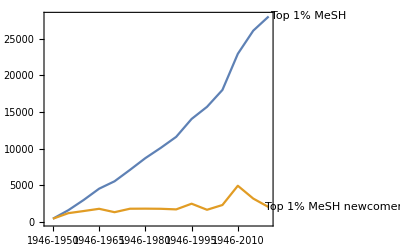

図6

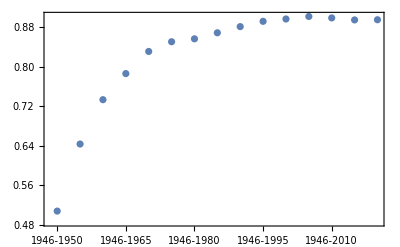

図7

### 6. 累積年代ごとのレファレンスネットワークの変化

#### 6.1 累積年代ごとのレファレンスネットワーク構造

ここでは純粋なレファレンスによるネットワーク構造の変化を計量的に観察する。累積年代ごとのレファレンスネットワークより弱連結グラフ（Weakly connected Graph: 
WCG）を構成した。弱連結グラフとは共引用もしくは書誌結合によって連結される論文集合である。その他各グラフの累積年代ごとの特徴量を表8にを示す。この表のはレファレンス情報をもとに構成しているため、レファレンスを持たず引用もされない論文は集計されていない。そこで「Largest WCG vertices % (all articles)」には全論文から再計算した割合を示す。Zipfの係数aについても全論文から再計算したがほぼ変化が見られなかったため記載していない。

全体の傾向として累積年代が進むに伴いWCGの数も増加するが最大WCGのメンバー数も急増する。この相乗効果によりグループを構成するメンバー数の差はより顕著になる。このことはZipfの係数aが累積年代が進むごとに増加していることからもわかる。一方で最大WCGのサイズ（論文数）も累積年代が進むにつれ増加し、2020にはそのメンバー数は全論文の3割に達している。

表8

累積年代ごとのレファレンスネットワークの属性:

論文数、WCG数、最大WCGにおける論文数（そのパーセンテージ）、すべての論文を対象にした場合の最大WCGにおける論文数のパーセンテージ、WCGを構成する論文数におけるZipfの係数a。

ここでの論文数にはレファレンスを持たず引用されない論文は含まれない。

Generation | Total vertices | WCG | Largest WCG vertices | Largest WCG vertices % | Largest WCG vertices % (all articles) | Zipf's a
1946-1950 | 25659 | 2353 | 17910 | 69.8 | 2.7 | 7.51
1946-1955 | 106865 | 3851 | 94830 | 88.7 | 5.5 | 11.26
1946-1960 | 230664 | 4624 | 216474 | 93.8 | 7.6 | 12.1
1946-1965 | 387646 | 5729 | 370660 | 95.6 | 8.7 | 13.4
1946-1970 | 635815 | 7020 | 615244 | 96.8 | 9.7 | 13.94
1946-1975 | 991194 | 8446 | 966113 | 97.5 | 11.2 | 13.13
1946-1980 | 1452803 | 9401 | 1425267 | 98.1 | 12.6 | 13.7
1946-1985 | 2022734 | 10026 | 1993398 | 98.5 | 13.8 | 14.18
1946-1990 | 2761367 | 10687 | 2730892 | 98.9 | 14.9 | 14.7
1946-1995 | 3715190 | 11361 | 3683220 | 99.1 | 16.3 | 15.4
1946-2000 | 4704818 | 12147 | 4670358 | 99.3 | 17.1 | 15.4
1946-2005 | 6388248 | 13000 | 6351561 | 99.4 | 19.1 | 17.27
1946-2010 | 9604916 | 13398 | 9568400 | 99.6 | 23.4 | 17.87
1946-2015 | 14351433 | 13643 | 14315982 | 99.8 | 28.2 | 18.64
1946-2020 | 20271870 | 14933 | 20235562 | 99.8 | 32.2 | 19.1

#### 6.2 累積年代ごとのレファレンスネットワークの変化

この章ではレファレンスネットワークの変化をトレンドによってとらえる。まず、「レファレンスネットワークの変化」とそのトレンドを定義する。レファレンスネットワークの変化とは、ある世代のネットワークと次の世代のレファレンスネットワークの差分とする。「レファレンスネットワークの変化におけるトレンド」とは、レファレンスネットワークの差分に含まれるトレンド、すなわちその差分を構成する主要論文・主要雑誌・主要テーマとする。

## 考察

### 1. 収録の変化

本研究では75年間にわたる収録期間を対象としているため、収録ポリシーの変更など学術活動とは異なる要因による変化が含まれている。この傍証としてはZipfの係数の変化が挙げられる。一般的に学術的生産にかかるZipfの係数変化は増加傾向をなすと考えられるが、図3では1980を前後として上昇傾向から下降傾向へと急激に変化しており何らかの収録上の要因によるものと思われる。

論文の収録数は2005ころから急激な上昇が見られ、新規主要論文の出現においも2010より急激な上昇がみられる。このことは収録対象が急速に拡大したためと思われるが、ポリシーの変更等ではなく実際の雑誌の新生、あるいは各雑誌における収録論文数の増加を反映したものであるかもしれない。

一方、本研究では研究トレンドの分析にMeSHを用いているため、HeSHの変更・追加は本研究の分析に大きく影響するが、NLMでは伝統的に遡及的な変更を行うため、年代によよる差異という影響は少ないと考えられる。すなわち、本研究の主眼である研究トレンドの「変化」という視点においては一定の視点からの分析が行われたと考えて良いであろう。

### 2. 研究トレンドの変化

表6および表7ともに主要なテーマはほとんどすべて生化学・分子生物学に関するもので、しかもかなり一般的なターム（Humans、Animals、Proteinsなど）として現れている。表6（主要論文）に特徴的に見られるタームとして、Epoxy Resins、Molybdenum、Tungstenといったものがあり歯学にかかるテーマであると推察される。

### 3. レファレンスネットワークの変化

## 参考

Leydesdorf, L. Various methods for the mapping of science. Scientometrics. 1987, Vol. 11, Nos 5-6, p. 295-324.

Leydesdorf, L. Clusters and maps of science journals based on bi-connected graphs in Journal Citation Reports. Journal of Docu- mentation. 2004, Vol. 60, No. 4, p. 371-427.

Leydesdorf, L. Indicators of structual change in the dynamics of science: Entropy statisitics of the SCI Journal Citation Re- ports. Scientometrics. 2002, Vol. 53, No. 1, p. 131-159.

Leydesdorf L. Can scientific journals be classified in terms of aggregated journal- journal citation relations using the Journal Citation Reports? Journal of the American Society for Information Science and Tech- nology. 2006, Vol. 57, No. 5, p. 601-613.

天野晃;児玉閲;柴田大輔;小野寺夏生. 引用データに基づく自然科学領域における学術研究分野間の関係. 情報メディア研究. 2013, Vol 12, No. 1, p. 28-41.

天野晃;児玉閲. 引用にもとづく雑誌クラスタリング法の開発. 情報メディア研究. 2008, Vol 7, No. 1, p. 63-73.

Li

https://pubmed.ncbi.nlm.nih.gov/ . (accessed 2024.07.01)

## 検討

Essential journalsの過去のIF <- 困難

Clustering -> 可視化が困難なのでクラスタリングで工夫するしかない

article <- 困難かも

cited/citing

MeSH

journal

cited/citing

MeSH

MeSH

article cited/citing

article内共出現

Network成長の可視化 (reference) <- なんらかの捨象・クラスタリングが必要 -> 難しい

article

Journal

MeSH

Essential articlesが構成する「Essential network」を抽出できるか？

グラフ(vertex)の差分に注目する

top 1%を元にネットワークを再構築する

メンバーのtop1%を考慮する

表6、7のタームの頻度を考慮する